```mathematica
Get["C:\\Users\\Aleks\\OneDrive\\Študij 3. letnik\\Napredna računalniška orodja\\Mathematica\\funk.m"]
```

```mathematica
n =10000; (**Število generiranih točk**)
z=funk[n];(**Funkcijska datoteka, vrne: indeks 1-približek, 2-koordinate točk znotraj kroga, 3-koordinate točk zunaj kroga**)
Print["Približek π pri ", n ," točkah je: ",z[[1]]]
```

Približek π pri 10000 točkah je: 3.1532

```mathematica
funk2[nmax_]:=Module[{n},For[n=10,n<nmax,n*=10,
Print["Razlika pri ",n," točkah je: ",Abs[N[Pi]-funk[n][[1]]]](**s funkcijo za računanje približka π ponovno generira točke, izračuna π in jih primerja z vrednostjo iz Mathematice**)
]]
funk2[10000]
```

Razlika pri 10 točkah je: 0.0584073

Razlika pri 100 točkah je: 0.141593

Razlika pri 1000 točkah je: 0.0344073

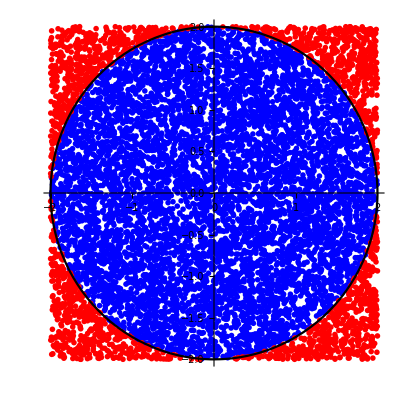

```mathematica
in=ListPlot[z[[2]],PlotMarkers->x,PlotStyle->Blue];
out=ListPlot[z[[3]],PlotMarkers->x,PlotStyle->Red];
krog=ContourPlot[x^2+y^2==4,{x,-2,2},{y,-2,2},ContourStyle->Black];
Show[{in,out,krog},PlotRange->{{-2,2},{-2,2}},AspectRatio->1]
```